```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];

];
{kglob,fglob}
]
```

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},
(*psis=GeneratePsis[order];*)
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};
];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
{psis,GradPhi,Jac,x,y}
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
fu=-1;
For[i=1,i≤ nnodes,i++,

ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order 4];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];
Print["elcoords = ",elcoords];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,topol_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];

(*nnodes=Length[allcoords] order;*)
sz= Length[nnodes]2;
Print["Nnodes = ",nnodes];
Print["Length[nnodes] = ",Length[nnodes]];
Print["sz= ",sz];
rows=order 4;
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;

{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineNewman[EF_,fx_,order_,nodes_,topol_,id1_,id2_,fxorfy_]:=Block[{Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,vecnodes,iel},
iel=Length[topol];
vecnodes={};
For[j=1,j≤iel,j++,
node={};
For[i=1,i≤order 4,i++,
(*Print["j = ",j];
Print["i = ",i];
Print["topol[[j,i]] = ",topol[[j,i]]];
Print["nodes[[ topol[[j,i]] ]]= ",nodes[[ topol[[j,i]] ]]];*)
If[nodes[[ topol[[j,i]] ]][[2]]==nodes[[id1]][[2]],
AppendTo[node,nodes[[ topol[[j,i]] ]]];
];
];
If[Length[node]≠0,
node=SortBy[node,Small];
AppendTo[vecnodes,node];
];
];
Print["vecnodes = ",vecnodes];
el=Length[vecnodes];

{elsw,ids}=DefineLineNodes[id1,id2,nodes];
fi=1;
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];

co=vecnodes[[el-i+fi]];
co=vecnodes[[i]];
Print["co = ",co];

newco=co;
xx=Sum[shapes[[i]] newco[[i]][[1]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Print["integralxi1 = ",integralxi1];
If[fxorfy==1,(*fy*)
Ef[[ ids[[i]] 2]]+=integralxi1[[1]];
Ef[[ ids[[i+1]] 2]]+=integralxi1[[2]];
Ef[[ ids[[i+3]] 2]]+=integralxi1[[3]];
,
(*fx*)
Ef[[ ids[[i]]2-1 ]]+=integralxi1[[1]];
Ef[[ ids[[i]]2 ]]+=integralxi1[[2]];
];
];
Ef
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
nnodes=Flatten[allcoords,1]
Length[nnodes]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[allcoords,1].

Flatten[allcoords,1]

2

{{2,1},{5,2},{4,6},{1,4}}

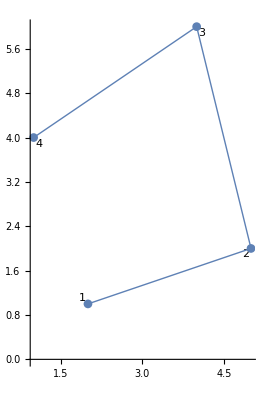

Nnodes = {{2,1},{5,2},{4,6},{1,4}}

Length[nnodes] = 4

sz= 8

KE = (0.407308 | 0.104864 | -0.30098 | -0.139536 | -0.0900181 | -0.115573 | -0.0163098 | 0.150245
0.104864 | 0.545967 | -0.0728695 | -0.0289742 | -0.115573 | -0.27669 | 0.0835784 | -0.240303
-0.30098 | -0.0728695 | 0.703151 | -0.142745 | 0.0516809 | 0.0812837 | -0.453852 | 0.134331
-0.139536 | -0.0289742 | -0.142745 | 0.394194 | 0.14795 | -0.182601 | 0.134331 | -0.182619
-0.0900181 | -0.115573 | 0.0516809 | 0.14795 | 0.316654 | 0.107924 | -0.278317 | -0.140301
-0.115573 | -0.27669 | 0.0812837 | -0.182601 | 0.107924 | 0.469031 | -0.0736345 | -0.00974016
-0.0163098 | 0.0835784 | -0.453852 | 0.134331 | -0.278317 | -0.0736345 | 0.748478 | -0.144275
0.150245 | -0.240303 | 0.134331 | -0.182619 | -0.140301 | -0.00974016 | -0.144275 | 0.432662)

FE = (0.
0
0.
0
0.
0
0.
0)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}};
topol={{1,2,3,4}};
nnodes=Flatten[allcoords,1]
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
{KE,FE}=Assemble[allcoords,topol,1,1];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

{{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5}}

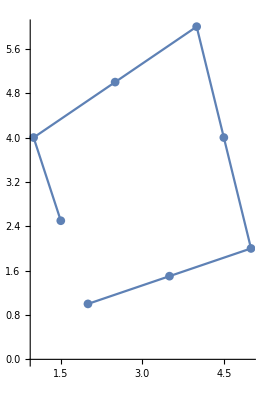

Nnodes = {{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5}}

Length[nnodes] = 8

sz= 16

KE = (-0.926209 | 0.167843 | -0.168083 | 0.0207932 | -0.329102 | 0.109389 | 3.60628 | -1.01791 | -1.03542 | 0.290414 | -0.864312 | 0.211402 | 0.881102 | -0.177928 | -2.52489 | 0.919757
0.167843 | -0.389864 | -0.00142898 | -0.0699519 | 0.109389 | -0.182697 | -0.99569 | 1.95312 | 0.379303 | -0.662144 | 0.211402 | -0.484511 | -0.177928 | 0.274053 | 0.830868 | -1.44345
-0.168083 | -0.00142898 | -0.50248 | 0.203432 | 0.513668 | -0.153472 | -0.396912 | 0.143917 | -0.927747 | 0.288716 | 1.48861 | -0.332797 | -0.20704 | -0.146782 | 0.413478 | -0.110339
0.0207932 | -0.0699519 | 0.203432 | -0.517203 | -0.175694 | 0.278184 | 0.143917 | -0.198799 | 0.199827 | -0.407726 | -0.243908 | 1.02057 | -0.146782 | -0.13077 | -0.110339 | 0.220474
-0.329102 | 0.109389 | 0.513668 | -0.175694 | -1.52616 | 0.541612 | 1.90253 | -0.584775 | -0.443354 | 0.0673247 | -0.727453 | 0.282098 | 0.494755 | -0.162631 | -0.0856686 | -0.0171107
0.109389 | -0.182697 | -0.153472 | 0.278184 | 0.541612 | -1.11649 | -0.606997 | 1.27998 | 0.0673247 | -0.181653 | 0.19321 | -0.194402 | -0.0737419 | 0.0838274 | -0.0171107 | -0.0601892
3.60628 | -0.99569 | -0.396912 | 0.143917 | 1.90253 | -0.606997 | -7.15576 | 1.87319 | 3.17397 | -0.826312 | 0.708278 | -0.341645 | -1.55452 | 0.462583 | 2.04265 | -0.362157
-1.01791 | 1.95312 | 0.143917 | -0.198799 | -0.584775 | 1.27998 | 1.87319 | -4.04148 | -0.826312 | 1.67752 | -0.341645 | 0.280007 | 0.373694 | -0.767634 | -0.273268 | 1.06701
-1.03542 | 0.379303 | -0.927747 | 0.199827 | -0.443354 | 0.0673247 | 3.17397 | -0.826312 | -0.293524 | -0.0369423 | 0.894803 | 0.0211223 | -0.0296472 | -0.000608477 | -4.95057 | 1.07957
0.290414 | -0.662144 | 0.288716 | -0.407726 | 0.0673247 | -0.181653 | -0.826312 | 1.67752 | -0.0369423 | -0.179899 | 0.0211223 | 0.294145 | -0.000608477 | -0.104956 | 1.07957 | -2.44449
-0.864312 | 0.211402 | 1.48861 | -0.243908 | -0.727453 | 0.19321 | 0.708278 | -0.341645 | 0.894803 | 0.0211223 | -4.23865 | 0.536153 | 2.33222 | -0.0912503 | 1.3395 | -0.487594
0.211402 | -0.484511 | -0.332797 | 1.02057 | 0.282098 | -0.194402 | -0.341645 | 0.280007 | 0.0211223 | 0.294145 | 0.536153 | -2.89164 | -0.0912503 | 1.86756 | -0.487594 | 0.951542
0.881102 | -0.177928 | -0.20704 | -0.146782 | 0.494755 | -0.0737419 | -1.55452 | 0.373694 | -0.0296472 | -0.000608477 | 2.33222 | -0.0912503 | -2.29241 | -0.000580036 | 0.991122 | -0.0525656
-0.177928 | 0.274053 | -0.146782 | -0.13077 | -0.162631 | 0.0838274 | 0.462583 | -0.767634 | -0.000608477 | -0.104956 | -0.0912503 | 1.86756 | -0.000580036 | -1.81827 | -0.0525656 | 0.698213
-2.52489 | 0.830868 | 0.413478 | -0.110339 | -0.0856686 | -0.0171107 | 2.04265 | -0.273268 | -4.95057 | 1.07957 | 1.3395 | -0.487594 | 0.991122 | -0.0525656 | 5.4454 | -1.56023
0.919757 | -1.44345 | -0.110339 | 0.220474 | -0.0171107 | -0.0601892 | -0.362157 | 1.06701 | 1.07957 | -2.44449 | -0.487594 | 0.951542 | -0.0525656 | 0.698213 | -1.56023 | 2.34369)

FE = (0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0)

```mathematica
order=2;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5}}};
topol={{1,2,3,4,5,6,7,8}};
nnodes=Flatten[allcoords,1]
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

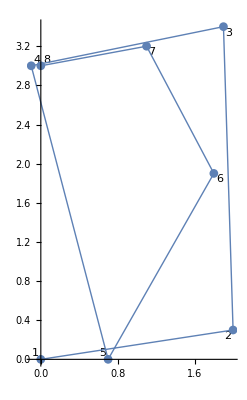

Nnodes = {{0,0},{2,0.3},{1.9,3.4},{-0.1,3},{0.7,0},{1.8,1.9},{1.1,3.2},{0,3}}

Length[nnodes] = 8

sz= 16

```mathematica
order=2;
young=43;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

allcoords={{{0,0},{2,0.3},{1.9,3.4},{-0.1,3},{0.7,0},{1.8,1.9},{1.1,3.2},{0,3}}};
topol={{1,2,3,4,5,6,7,8}};

nnodes=Flatten[allcoords,1];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]

forcing=0;
{KE,FE}=Assemble[allcoords,topol,order,forcing];
```

{{0,0},{10,0},{10,6},{0,6}}

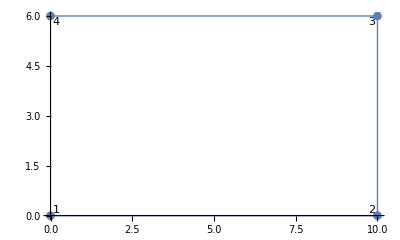

Nnodes = {{0,0},{10,0},{10,6},{0,6}}

Length[nnodes] = 4

sz= 8

KE = (4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

FE = (0.
0
0.
0
0.
0
0.
0)

8

KE = (4.33455×10^18 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^18 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^18 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^18 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

FE = (0
0
6000
0
6000.
0
0
0)

(0
0
0.002
0
0.002
-0.00036
0
-0.00036)

{6.92113×10^-13,0.,11.,1.21149×10^-28,11.,5.82,6.92113×10^-13,5.82}

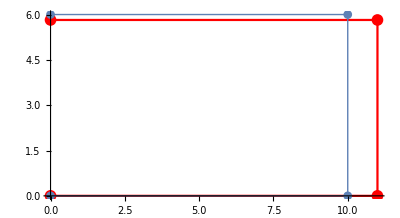

```mathematica
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{10,0},{10,6},{0,6}}};
topol={{1,2,3,4}};
nnodes=Flatten[allcoords,1]
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]

forcing=0;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{10^12,1},{1,1}},{0,0}];

(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{6000,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{6000,0}];



Length[KE]
Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

sol=LinearSolve[KE,FE,Method->"Cholesky"];
Chop[sol]//MatrixForm
scale=500;
deformed=(Flatten[nnodes]+scale sol)

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

{{0,0},{10,0},{10,6},{0,6},{5,0},{10,3},{5,6},{0,3}}

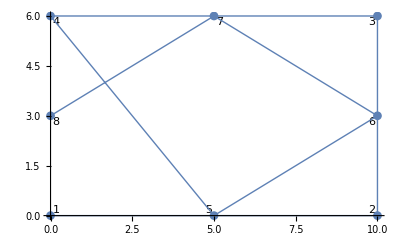

Nnodes = {{0,0},{10,0},{10,6},{0,6},{5,0},{10,3},{5,6},{0,3}}

Length[nnodes] = 8

sz= 16

KE = (4.94902×10^6 | -925194. | 24788.4 | 192368. | -213463. | -157360. | 1433.24 | 100793. | -581138. | -630358. | -425463. | -240569. | -388389. | -240569. | -510452. | -264058.
-925194. | 7.84873×10^6 | 100793. | -999826. | -157360. | -338534. | 192368. | 1.04141×10^6 | -264058. | 2.2234×10^6 | -240569. | 974790. | -240569. | -2.26549×10^6 | -630358. | -3.95457×10^6
24788.4 | 100793. | 2.62816×10^6 | -1.79171×10^6 | 2.22211×10^6 | 340338. | -468746. | 177587. | -1.17757×10^7 | 4.27113×10^6 | 3.5343×10^6 | -1.57931×10^6 | -2.79567×10^6 | 508188. | -3.58644×10^6 | 625986.
192368. | -999826. | -1.79171×10^6 | 5.42219×10^6 | 248763. | 3.9102×10^6 | 177587. | -743392. | 3.90483×10^6 | -9.46658×10^6 | -1.21301×10^6 | -2.95052×10^6 | 508188. | -2.52792×10^6 | 625986. | -4.43226×10^6
-213463. | -157360. | 2.22211×10^6 | 248763. | 2.19887×10^6 | 3.50073×10^6 | 2.23078×10^6 | 340338. | 5.76631×10^6 | -217078. | -4.12654×10^6 | -1.87785×10^6 | -4.15739×10^6 | -2.24415×10^6 | 5.71876×10^6 | -217078.
-157360. | -338534. | 340338. | 3.9102×10^6 | 3.50073×10^6 | 3.48723×10^6 | 248763. | 3.15171×10^6 | -217078. | 7.02921×10^6 | -2.24415×10^6 | -7.91722×10^6 | -1.87785×10^6 | -5.22039×10^6 | -217078. | 1.11851×10^7
1433.24 | 192368. | -468746. | 177587. | 2.23078×10^6 | 248763. | 2.65635×10^6 | -1.79171×10^6 | -3.55822×10^6 | 625986. | -2.75283×10^6 | 508188. | 3.34201×10^6 | -1.21301×10^6 | -1.15687×10^7 | 3.90483×10^6
100793. | 1.04141×10^6 | 177587. | -743392. | 340338. | 3.15171×10^6 | -1.79171×10^6 | 2.9586×10^6 | 625986. | -6.89857×10^6 | 508188. | -6.27153×10^6 | -1.57931×10^6 | 1.38558×10^7 | 4.27113×10^6 | -2.75556×10^7
-581138. | -264058. | -1.17757×10^7 | 3.90483×10^6 | 5.76631×10^6 | -217078. | -3.55822×10^6 | 625986. | 6.0215×10^6 | -8.13491×10^6 | 3.98865×10^6 | -2.17106×10^6 | -1.98008×10^6 | -26693.1 | -1.29917×10^7 | 1.40662×10^6
-630358. | 2.2234×10^6 | 4.27113×10^6 | -9.46658×10^6 | -217078. | 7.02921×10^6 | 625986. | -6.89857×10^6 | -8.13491×10^6 | 6.87957×10^6 | -2.17106×10^6 | 22658.9 | -26693.1 | -2.05013×10^6 | 1.40662×10^6 | -2.06037×10^7
-425463. | -240569. | 3.5343×10^6 | -1.21301×10^6 | -4.12654×10^6 | -2.24415×10^6 | -2.75283×10^6 | 508188. | 3.98865×10^6 | -2.17106×10^6 | -1.24675×10^6 | 3.42551×10^6 | 8.48053×10^6 | 2.23436×10^6 | -1.95558×10^6 | -26693.1
-240569. | 974790. | -1.57931×10^6 | -2.95052×10^6 | -1.87785×10^6 | -7.91722×10^6 | 508188. | -6.27153×10^6 | -2.17106×10^6 | 22658.9 | 3.42551×10^6 | 5.67017×10^6 | 2.23436×10^6 | 1.34494×10^7 | -26693.1 | -4.19149×10^6
-388389. | -240569. | -2.79567×10^6 | 508188. | -4.15739×10^6 | -1.87785×10^6 | 3.34201×10^6 | -1.57931×10^6 | -1.98008×10^6 | -26693.1 | 8.48053×10^6 | 2.23436×10^6 | -1.07487×10^6 | 3.42551×10^6 | 3.84698×10^6 | -2.17106×10^6
-240569. | -2.26549×10^6 | 508188. | -2.52792×10^6 | -2.24415×10^6 | -5.22039×10^6 | -1.21301×10^6 | 1.38558×10^7 | -26693.1 | -2.05013×10^6 | 2.23436×10^6 | 1.34494×10^7 | 3.42551×10^6 | -9.35206×10^6 | -2.17106×10^6 | 1.2404×10^7
-510452. | -630358. | -3.58644×10^6 | 625986. | 5.71876×10^6 | -217078. | -1.15687×10^7 | 4.27113×10^6 | -1.29917×10^7 | 1.40662×10^6 | -1.95558×10^6 | -26693.1 | 3.84698×10^6 | -2.17106×10^6 | 5.96149×10^6 | -8.13491×10^6
-264058. | -3.95457×10^6 | 625986. | -4.43226×10^6 | -217078. | 1.11851×10^7 | 3.90483×10^6 | -2.75556×10^7 | 1.40662×10^6 | -2.06037×10^7 | -26693.1 | -4.19149×10^6 | -2.17106×10^6 | 1.2404×10^7 | -8.13491×10^6 | 1.21245×10^7)

FE = (0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0)

16

KE = (4.94902×10^18 | -925194. | 24788.4 | 192368. | -213463. | -157360. | 1433.24 | 100793. | -581138. | -630358. | -425463. | -240569. | -388389. | -240569. | -510452. | -264058.
-925194. | 7.84873×10^18 | 100793. | -999826. | -157360. | -338534. | 192368. | 1.04141×10^6 | -264058. | 2.2234×10^6 | -240569. | 974790. | -240569. | -2.26549×10^6 | -630358. | -3.95457×10^6
24788.4 | 100793. | 2.62816×10^6 | -1.79171×10^6 | 2.22211×10^6 | 340338. | -468746. | 177587. | -1.17757×10^7 | 4.27113×10^6 | 3.5343×10^6 | -1.57931×10^6 | -2.79567×10^6 | 508188. | -3.58644×10^6 | 625986.
192368. | -999826. | -1.79171×10^6 | 5.42219×10^18 | 248763. | 3.9102×10^6 | 177587. | -743392. | 3.90483×10^6 | -9.46658×10^6 | -1.21301×10^6 | -2.95052×10^6 | 508188. | -2.52792×10^6 | 625986. | -4.43226×10^6
-213463. | -157360. | 2.22211×10^6 | 248763. | 2.19887×10^6 | 3.50073×10^6 | 2.23078×10^6 | 340338. | 5.76631×10^6 | -217078. | -4.12654×10^6 | -1.87785×10^6 | -4.15739×10^6 | -2.24415×10^6 | 5.71876×10^6 | -217078.
-157360. | -338534. | 340338. | 3.9102×10^6 | 3.50073×10^6 | 3.48723×10^6 | 248763. | 3.15171×10^6 | -217078. | 7.02921×10^6 | -2.24415×10^6 | -7.91722×10^6 | -1.87785×10^6 | -5.22039×10^6 | -217078. | 1.11851×10^7
1433.24 | 192368. | -468746. | 177587. | 2.23078×10^6 | 248763. | 2.65635×10^18 | -1.79171×10^6 | -3.55822×10^6 | 625986. | -2.75283×10^6 | 508188. | 3.34201×10^6 | -1.21301×10^6 | -1.15687×10^7 | 3.90483×10^6
100793. | 1.04141×10^6 | 177587. | -743392. | 340338. | 3.15171×10^6 | -1.79171×10^6 | 2.9586×10^6 | 625986. | -6.89857×10^6 | 508188. | -6.27153×10^6 | -1.57931×10^6 | 1.38558×10^7 | 4.27113×10^6 | -2.75556×10^7
-581138. | -264058. | -1.17757×10^7 | 3.90483×10^6 | 5.76631×10^6 | -217078. | -3.55822×10^6 | 625986. | 6.0215×10^6 | -8.13491×10^6 | 3.98865×10^6 | -2.17106×10^6 | -1.98008×10^6 | -26693.1 | -1.29917×10^7 | 1.40662×10^6
-630358. | 2.2234×10^6 | 4.27113×10^6 | -9.46658×10^6 | -217078. | 7.02921×10^6 | 625986. | -6.89857×10^6 | -8.13491×10^6 | 6.87957×10^18 | -2.17106×10^6 | 22658.9 | -26693.1 | -2.05013×10^6 | 1.40662×10^6 | -2.06037×10^7
-425463. | -240569. | 3.5343×10^6 | -1.21301×10^6 | -4.12654×10^6 | -2.24415×10^6 | -2.75283×10^6 | 508188. | 3.98865×10^6 | -2.17106×10^6 | -1.24675×10^6 | 3.42551×10^6 | 8.48053×10^6 | 2.23436×10^6 | -1.95558×10^6 | -26693.1
-240569. | 974790. | -1.57931×10^6 | -2.95052×10^6 | -1.87785×10^6 | -7.91722×10^6 | 508188. | -6.27153×10^6 | -2.17106×10^6 | 22658.9 | 3.42551×10^6 | 5.67017×10^6 | 2.23436×10^6 | 1.34494×10^7 | -26693.1 | -4.19149×10^6
-388389. | -240569. | -2.79567×10^6 | 508188. | -4.15739×10^6 | -1.87785×10^6 | 3.34201×10^6 | -1.57931×10^6 | -1.98008×10^6 | -26693.1 | 8.48053×10^6 | 2.23436×10^6 | -1.07487×10^6 | 3.42551×10^6 | 3.84698×10^6 | -2.17106×10^6
-240569. | -2.26549×10^6 | 508188. | -2.52792×10^6 | -2.24415×10^6 | -5.22039×10^6 | -1.21301×10^6 | 1.38558×10^7 | -26693.1 | -2.05013×10^6 | 2.23436×10^6 | 1.34494×10^7 | 3.42551×10^6 | -9.35206×10^6 | -2.17106×10^6 | 1.2404×10^7
-510452. | -630358. | -3.58644×10^6 | 625986. | 5.71876×10^6 | -217078. | -1.15687×10^7 | 4.27113×10^6 | -1.29917×10^7 | 1.40662×10^6 | -1.95558×10^6 | -26693.1 | 3.84698×10^6 | -2.17106×10^6 | 5.96149×10^18 | -8.13491×10^6
-264058. | -3.95457×10^6 | 625986. | -4.43226×10^6 | -217078. | 1.11851×10^7 | 3.90483×10^6 | -2.75556×10^7 | 1.40662×10^6 | -2.06037×10^7 | -26693.1 | -4.19149×10^6 | -2.17106×10^6 | 1.2404×10^7 | -8.13491×10^6 | 1.21245×10^7)

FE = (0
0
4000
0
4000.
0
0
0
0
0
4000.
0
0.
0
0
0)

(0
0
0.00207902
0
0.00212208
-0.0004199
0
-0.000362953
0.0009559
0
0.00194972
-0.0000293082
0.000487456
-0.000344287
0
-0.0001841)

{1.82646×10^-13,-1.78697×10^-14,11.0395,1.08914×10^-13,11.061,5.79005,5.92998×10^-13,5.81852,5.47795,-3.25312×10^-14,10.9749,2.98535,5.24373,5.82786,7.45632×10^-13,2.90795}

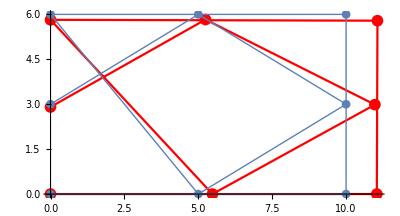

```mathematica
order=2;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{10,0},{10,6},{0,6},{5,0},{10,3},{5,6},{0,3}}};
topol={{1,2,3,4,5,6,7,8}};
nnodes=Flatten[allcoords,1]
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]

forcing=0;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,5,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,8,0,{{10^12,1},{1,1}},{0,0}];

(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{4000,0}];

(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,6,1,{{1,1},{1,1}},{4000,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{4000,0}];



Length[KE]
Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

sol=LinearSolve[KE,FE,Method->"Banded"];
Chop[sol]//MatrixForm
scale=500;
deformed=(Flatten[nnodes]+scale sol)

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
tabdeformed
nnodes
```

{{1.82646×10^-13,-1.78697×10^-14},{11.0395,1.08914×10^-13},{11.061,5.79005},{5.92998×10^-13,5.81852},{5.47795,-3.25312×10^-14},{10.9749,2.98535},{5.24373,5.82786},{7.45632×10^-13,2.90795}}

{{0,0},{10,0},{10,6},{0,6},{5,0},{10,3},{5,6},{0,3}}

QuadElement[{{1,2,3,4,5,6,7,8}}]

ElementMesh[{{0.,10.},{0.,6.}},{QuadElement[<1>]}]

ElementMesh[{{1.82646×10^-13,11.061},{-3.25312×10^-14,5.82786}},{QuadElement[<1>]}]

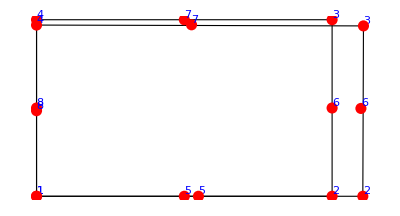

```mathematica
Needs["NDSolve`FEM`"]
q=QuadElement[topol]
mesh=ToElementMesh["Coordinates"->nnodes,"MeshElements"->{q}]
mesh2=ToElementMesh["Coordinates"->tabdeformed,"MeshElements"->{q}]
Show[mesh["Wireframe"],mesh2["Wireframe"],
mesh["Wireframe"["MeshElement" -> "PointElements", "MeshElementStyle"->Directive[Red,PointSize[0.02]],"MeshElementIDStyle"->Blue]],mesh2["Wireframe"["MeshElement" -> "PointElements", "MeshElementStyle"->Directive[Red,PointSize[0.02]],"MeshElementIDStyle"->Blue]]]
```

```mathematica
Length[allcoords]2
```

2

```mathematica
Count[allcoords]
```

Count[{{{0,0},{10,0},{10,6},{0,6},{5,0},{10,3},{5,6},{0,3}}}]

Nnodes = {{0.,0.},{2.,0.},{4.,0.},{6.,0.},{8.,0.},{8.,2.},{6.,2.},{4.,2.},{2.,2.},{0.,2.},{8.,4.},{6.,4.},{4.,4.},{2.,4.},{0.,4.}}

Length[nnodes] = 15

sz= 30

co = {8.,6.}

Co = {8.,6.}

ids[[i]] = 11

co = {6.,4.}

Co = {6.,4.}

ids[[i]] = 12

co = {4.,2.}

Co = {4.,2.}

ids[[i]] = 13

co = {2.,0.}

Co = {2.,0.}

ids[[i]] = 14

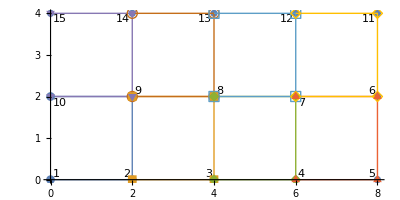

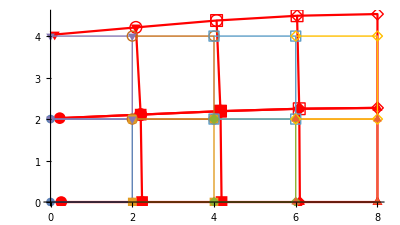

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{2,0},{2,2},{0,2}},{{2,0},{4,0},{4,2},{2,2}},{{4,0},{6,0},{6,2},{4,2}},{{6,0},{8,0},{8,2},{6,2}},{{0,2},{2,2},{2,4},{0,4}},{{2,2},{4,2},{4,4},{2,4}},{{4,2},{6,2},{6,4},{4,4}},{{6,2},{8,2},{8,4},{6,4}}};

topol={{1,2,9,10},{2,3,8,9},{3,4,7,8},{4,5,6,7},{10,9,14,15},{9,8,13,14},{8,7,12,13},{7,6,11,12}};

nnodes={{0.,0.},{2.,0.},{4.,0.},{6.,0.},{8.,0.},{8.,2.},{6.,2.},{4.,2.},{2.,2.},{0.,2.},{8.,4.},{6.,4.},{4.,4.},{2.,4.},{0.,4.}};
forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,5,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,5,11,{{10^12,1},{1,1}},{0,0}];

q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,15,11,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{2,0},{2,2},{0,2}},{{2,0},{4,0},{4,2},{2,2}},{{4,0},{6,0},{6,2},{4,2}},{{6,0},{8,0},{8,2},{6,2}},{{0,2},{2,2},{2,4},{0,4}},{{2,2},{4,2},{4,4},{2,4}},{{4,2},{6,2},{6,4},{4,4}},{{6,2},{8,2},{8,4},{6,4}}};

topol={{1,2,9,10},{2,3,8,9},{3,4,7,8},{4,5,6,7},{10,9,14,15},{9,8,13,14},{8,7,12,13},{7,6,11,12}};

nnodes={{0.,0.},{2.,0.},{4.,0.},{6.,0.},{8.,0.},{8.,2.},{6.,2.},{4.,2.},{2.,2.},{0.,2.},{8.,4.},{6.,4.},{4.,4.},{2.,4.},{0.,4.}};
forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,5,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,5,11,{{10^12,1},{1,1}},{0,0}];

q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,15,11,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

Nnodes = {{0.,0.},{2.,0.},{4.,0.},{6.,0.},{8.,0.},{8.,2.},{6.,2.},{4.,2.},{2.,2.},{0.,2.},{8.,4.},{6.,4.},{4.,4.},{2.,4.},{0.,4.}}

Length[nnodes] = 15

sz= 30

co = {8.,6.}

Co = {8.,6.}

ids[[i]] = 11

co = {6.,4.}

Co = {6.,4.}

ids[[i]] = 12

co = {4.,2.}

Co = {4.,2.}

ids[[i]] = 13

co = {2.,0.}

Co = {2.,0.}

ids[[i]] = 14

-Graphics-

-Graphics-

```mathematica
topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidels-ex1.txt","Table"],1]
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidnodes-ex1.txt","Table"][[;;,2;;]]
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}]
```

{{4,1,5,8,3,2,6,7},{5,13,17,8,10,15,11,6},{30,37,35,26,33,36,31,28},{35,32,24,26,34,29,25,31},{17,23,18,8,20,21,12,11},{4,8,18,14,7,12,16,9},{24,14,18,26,19,16,22,25},{26,18,23,30,22,21,27,28}}

{{8,0},{8,1},{7,0},{6,0},{8,2},{6.99496,2.00285},{5.99496,1.00285},{5.98992,2.0057},{5,0},{8,3},{5.99496,3.00285},{4.99184,2.00478},{8,4},{4,0},{7,4},{3.99688,1.00193},{6,4},{3.99376,2.00386},{3,0},{5,4},{3.99688,3.00193},{3.00112,1.99892},{4,4},{2,0},{2.00424,0.99699},{2.00848,1.99398},{3,4},{2.00424,2.99699},{1,0},{2,4},{1.00424,1.99699},{0,0},{1,4},{0,1},{0,2},{0,3},{0,4}}

{{{6,0},{8,0},{8,2},{5.98992,2.0057},{7,0},{8,1},{6.99496,2.00285},{5.99496,1.00285}},{{8,2},{8,4},{6,4},{5.98992,2.0057},{8,3},{7,4},{5.99496,3.00285},{6.99496,2.00285}},{{2,4},{0,4},{0,2},{2.00848,1.99398},{1,4},{0,3},{1.00424,1.99699},{2.00424,2.99699}},{{0,2},{0,0},{2,0},{2.00848,1.99398},{0,1},{1,0},{2.00424,0.99699},{1.00424,1.99699}},{{6,4},{4,4},{3.99376,2.00386},{5.98992,2.0057},{5,4},{3.99688,3.00193},{4.99184,2.00478},{5.99496,3.00285}},{{6,0},{5.98992,2.0057},{3.99376,2.00386},{4,0},{5.99496,1.00285},{4.99184,2.00478},{3.99688,1.00193},{5,0}},{{2,0},{4,0},{3.99376,2.00386},{2.00848,1.99398},{3,0},{3.99688,1.00193},{3.00112,1.99892},{2.00424,0.99699}},{{2.00848,1.99398},{3.99376,2.00386},{4,4},{2,4},{3.00112,1.99892},{3.99688,3.00193},{3,4},{2.00424,2.99699}}}

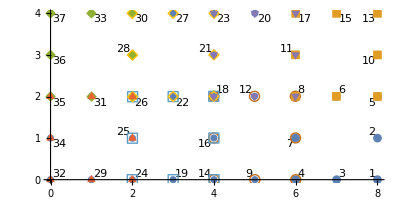

Nnodes = {{8,0},{8,1},{7,0},{6,0},{8,2},{6.99496,2.00285},{5.99496,1.00285},{5.98992,2.0057},{5,0},{8,3},{5.99496,3.00285},{4.99184,2.00478},{8,4},{4,0},{7,4},{3.99688,1.00193},{6,4},{3.99376,2.00386},{3,0},{5,4},{3.99688,3.00193},{3.00112,1.99892},{4,4},{2,0},{2.00424,0.99699},{2.00848,1.99398},{3,4},{2.00424,2.99699},{1,0},{2,4},{1.00424,1.99699},{0,0},{1,4},{0,1},{0,2},{0,3},{0,4}}

Length[nnodes] = 37

sz= 74

vecnodes = {{{6,4},{7,4},{8,4}},{{0,4},{1,4},{2,4}},{{4,4},{5,4},{6,4}},{{2,4},{3,4},{4,4}}}

co = {{6,4},{7,4},{8,4}}

integralxi1 = {-31.0436,-130.268,-33.5875}

co = {{0,4},{1,4},{2,4}}

integralxi1 = {-0.0334591,-25.9119,-12.8225}

co = {{4,4},{5,4},{6,4}}

integralxi1 = {-23.7736,-110.436,-31.018}

co = {{2,4},{3,4},{4,4}}

integralxi1 = {-12.8843,-73.7908,-23.7263}

(0
0
0
0
0
0
0
0
0
0
0.
0
0.
0
0.
0
0
0
0
0
0.
0
0.
0
0
-31.0436
0
0
0.
-130.301
0.
0
0.
-49.6855
0.
0
0
0
0.
-156.908
0.
0
0.
0
0.
-86.6133
0
0
0.
0
0.
0
0.
-31.018
0.
0
0
0
0.
-23.7263
0.
0
0
0
0.
0
0.
0
0.
0
0.
0
0.
0)

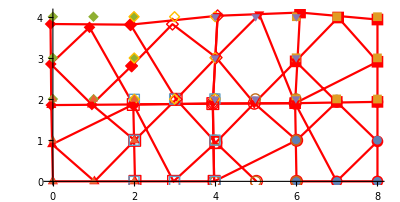

```mathematica
order=2;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidels-ex1.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidnodes-ex1.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListPlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,32,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,29,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,24,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,19,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,14,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,9,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{1,1},{1,10^12}},{0,0}];
(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,3,0,{{1,1},{1,10^12}},{0,0}];
(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{1,1},{1,10^12}},{0,0}];
(*Dirichlet -  vy=0 no no 2*)


(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,5,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,10,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,13,0,{{10^12,1},{1,1}},{0,0}];


q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,topol,37,13,1];
FE//MatrixForm

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=10000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];
tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
sol//Chop
```

{0,0,0,-2.9071×10^-6,-5.71676×10^-7,0,5.01556×10^-7,0,0,-6.87846×10^-6,2.26407×10^-7,-7.32632×10^-6,1.35677×10^-6,-5.04753×10^-7,-1.9339×10^-6,-0.0000106423,1.76311×10^-6,0,0,-9.38202×10^-6,-1.15194×10^-6,-8.70788×10^-6,-2.90534×10^-6,-0.0000107193,0,-6.85401×10^-6,-2.54402×10^-6,0,3.14337×10^-6,-1.92516×10^-6,1.90057×10^-6,-5.99908×10^-6,9.16733×10^-6,0.0000101867,-5.17254×10^-6,-0.0000114638,-2.61264×10^-6,0,8.65405×10^-6,5.86304×10^-6,2.80224×10^-6,5.72646×10^-7,3.69833×10^-6,-6.00273×10^-7,6.00906×10^-6,2.29554×10^-6,2.36243×10^-6,0,1.15974×10^-6,-3.13784×10^-8,-2.7335×10^-6,-0.0000125787,-5.30692×10^-6,-0.0000181209,-6.41462×10^-6,-0.0000192027,2.65323×10^-6,0,-8.6498×10^-6,-0.0000193165,-4.28576×10^-6,-0.0000130443,0,0,-9.79691×10^-6,-0.0000257711,-1.90319×10^-6,-9.84839×10^-6,-3.96813×10^-6,-0.0000146599,-5.24102×10^-6,-0.0000148995,-5.79214×10^-6,-0.0000177361}

```mathematica
Sum[FE[[i]],{i,1,Length[FE]}]
```

-509.296

```mathematica
Integrate[f[x],{x,0,8.}]
```

-509.296

```mathematica
KE.sol-FE//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Chop[sol]//MatrixForm
```

(0
0
0
-2.9071×10^-6
-5.71676×10^-7
0
5.01556×10^-7
0
0
-6.87846×10^-6
2.26407×10^-7
-7.32632×10^-6
1.35677×10^-6
-5.04753×10^-7
-1.9339×10^-6
-0.0000106423
1.76311×10^-6
0
0
-9.38202×10^-6
-1.15194×10^-6
-8.70788×10^-6
-2.90534×10^-6
-0.0000107193
0
-6.85401×10^-6
-2.54402×10^-6
0
3.14337×10^-6
-1.92516×10^-6
1.90057×10^-6
-5.99908×10^-6
9.16733×10^-6
0.0000101867
-5.17254×10^-6
-0.0000114638
-2.61264×10^-6
0
8.65405×10^-6
5.86304×10^-6
2.80224×10^-6
5.72646×10^-7
3.69833×10^-6
-6.00273×10^-7
6.00906×10^-6
2.29554×10^-6
2.36243×10^-6
0
1.15974×10^-6
-3.13784×10^-8
-2.7335×10^-6
-0.0000125787
-5.30692×10^-6
-0.0000181209
-6.41462×10^-6
-0.0000192027
2.65323×10^-6
0
-8.6498×10^-6
-0.0000193165
-4.28576×10^-6
-0.0000130443
0
0
-9.79691×10^-6
-0.0000257711
-1.90319×10^-6
-9.84839×10^-6
-3.96813×10^-6
-0.0000146599
-5.24102×10^-6
-0.0000148995
-5.79214×10^-6
-0.0000177361)

```mathematica
sol[[13 2+1]]
```

-2.54402×10^-6

```mathematica
Max[Abs[sol]]
```

0.0000257711

```mathematica
0.53085/40000
```

0.0000132713

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_]:=Block[{nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac},
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};
];
nels=Length[topol];
sol=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

For[j=1,j≤4 order,j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
];

For[j=1,j≤4 order,j++,
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] DetJac);
sol[[i,2]]+=(psis[[j]] coefs[[2id]] DetJac);

(*duxdx*)
dsol[[i,1]]+=(D[psis[[j]],xi] coefs[[2 id-1]] DetJac);
(*duxdy*)
dsol[[i,2]]+=(D[psis[[j]],eta] coefs[[2id-1]] DetJac);
(*duydx*)
dsol[[i,3]]+=(D[psis[[j]],xi] coefs[[2id]] DetJac);
(*duydy*)
dsol[[i,4]]+=(D[psis[[j]],eta] coefs[[2id]] DetJac);
(*Print["j+k = ",j+k];
Print["j = ",j];*)
];

];
{sol,dsol}
]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

eps=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.{ex,ey,exy};
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,eps}
];
```

```mathematica
solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],30 10^6,0.30][[1]];
```

{{1},{1}}
 |  |  |  |

{{3.2967×10^7 (10+1.58228×10^-20 (eta+eta^2) (1+2 xi) (1))+9.89011×10^6 (1),9.89011×10^6 (1)+3.2967×10^7 (1),1.15385×10^7 (1)},6,{3.2967×10^7 (-6.86381×10^-7 (1-eta^2) (19+7.10543×10^-15 eta xi^3+1.99804×10^-15 eta^2 xi^3)+1+5+1-7.68043×10^-7 (eta+eta^2) (1+2 xi) (19+1+1.99804×10^-15 eta^2 xi^3))+21 1,1,1}}
 |  |  |  |

```mathematica
stress[[8]]/.{xi->0,eta->0}
```

{-29.2698,166.719,-34.8537}